Begin by defining our system of replicator equations using the old method:

```mathematica
System1[γ_, Γ_, α_, g_, s_, u0_, v0_, p0_]:={u'[t]==s (-1+α) (γ-Γ) (p[t]-v[t]) (-1+u[t]) u[t],v'[t]==v[t] (-g^2 (-1+p[t]+v[t])+g α (-1+p[t]+v[t])+s (s (-1+p[t]+v[t])-α γ (-1+v[t]+(1+p[t]-v[t]) u[t])+α Γ (p[t] (-1+u[t])+u[t]-v[t] u[t]))),p'[t]==p[t] (-g^2 (-1+p[t]+v[t])+g α (-1+p[t]+v[t])+s (s (-1+p[t]+v[t])+α (Γ-Γ p[t]-γ v[t]-(γ-Γ) (-1+p[t]-v[t]) u[t]))), u[0]==u0,v[0]==v0,p[0]==p0}
```

Solve here, specifying parameter values:

Let’s pick some values of each parameter:

```mathematica
sys = {0.5,0.4}
```

{0.5,0.4}

Now Plot:

```mathematica
Ans=NDSolve[System1[0.5, 1.5, 0.5, 0.5, 0.5, 0.5, 0.25, 0.26],{u[t],v[t],p[t]},{t,0,100}]
```

{{u[t]→InterpolatingFunction[…][t],v[t]→InterpolatingFunction[…][t],p[t]→InterpolatingFunction[…][t]}}

{u[t],v[t],p[t]}/.NDSolve[{u'[t]==0.25 (-1+u[t]) u[t] (p[t]-v[t]),v'[t]==v[t] (0.+0.5 (0.5 (-1+p[t]+v[t])-0.25 (-1+u[t] (1+p[t]-v[t])+v[t])+0.75 (p[t] (-1+u[t])+u[t]-u[t] v[t]))),p'[t]==p[t] (0.+0.5 (0.5 (1.5-1.5 p[t]+1. u[t] (-1+p[t]-v[t])-0.5 v[t])+0.5 (-1+p[t]+v[t]))),u[0]=={0.5,0.4},v[0]==0.25,p[0]==0.26},{u[t],v[t],p[t]},{t,0,100}]

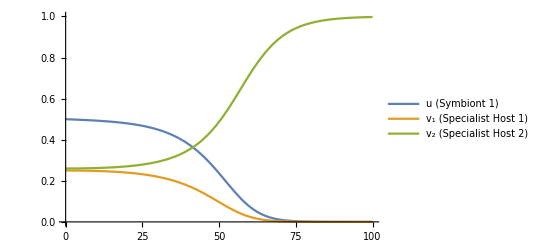

```mathematica
{uans,vans,pans}= {u[t],v[t],p[t]} /.Flatten[Ans]
graph = Plot[{uans,vans,pans},{t,0,100}, PlotRange -> {0,1}, PlotLegends->LineLegend[{"u (Symbiont 1)","v_1 (Specialist Host 1)","v_2 (Specialist Host 2)"}]]
```

Let’s try it parametrically:

```mathematica
ClearAll[t,α,γ,Γ,g,s,Ans,initial,v0,p0,u0,num,System2,interpolatingfunctions]
System2[γ_, Γ_, α_, g_, s_]:={u'[t]==s (-1+α) (γ-Γ) (p[t]-v[t]) (-1+u[t]) u[t],v'[t]==v[t] (-g^2 (-1+p[t]+v[t])+g α (-1+p[t]+v[t])+s (s (-1+p[t]+v[t])-α γ (-1+v[t]+(1+p[t]-v[t]) u[t])+α Γ (p[t] (-1+u[t])+u[t]-v[t] u[t]))),p'[t]==p[t] (-g^2 (-1+p[t]+v[t])+g α (-1+p[t]+v[t])+s (s (-1+p[t]+v[t])+α (Γ-Γ p[t]-γ v[t]-(γ-Γ) (-1+p[t]-v[t]) u[t]))), u[0]==u0,v[0]==v0,p[0]==p0}
```

Now substitute parameter values:

```mathematica
num =System2[0.1, 1.1, 0.5, 0.5, 0.5];
```

```mathematica
Ans=ParametricNDSolveValue[num,{u[t],v[t],p[t]},{t,0,100},{u0, v0, p0}];
```

Sweet that worked. Now let’s try some possible initial values of u:

```mathematica
initial = Table[{u0,v0,p0},{u0,{0,0.1,0.25,0.3,0,0.4,0.5,0.51,0.505,0.495,0.49,0.6,0.7,0.8,0.9,1}}, {v0,{0.25}},{p0,{0.25}}]~Flatten~2;
```

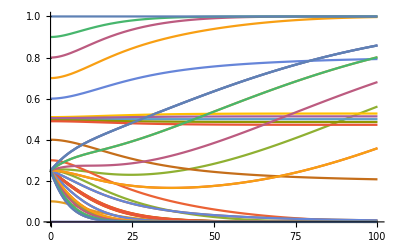

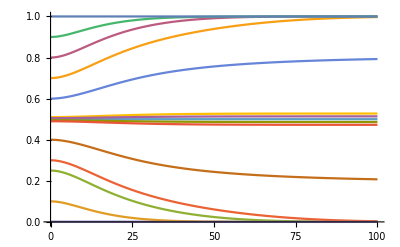

```mathematica
interpolatingfunctions=Ans@@@initial;
(*Host 1 frequencies are the second column of the interpolating function matrix. The symbiont is column1, specialist 2 is column 3*)
vseries =interpolatingfunctions[[All,2]];
Plot[interpolatingfunctions, {t,0,100}]
Plot[vseries,{t,0,100}]
```

Let’s try it slightly differently, this method ended up failing.

```mathematica
ClearAll[t,α,γ,Γ,g,s,Ans1,initial1,v0,p0,u0,num1,System3,interpolatingfunctions1]
System3[γ_, Γ_, α_, g_, s_, v0_,p0_]:={u'[t]==s (-1+α) (γ-Γ) (p[t]-v[t]) (-1+u[t]) u[t],v'[t]==v[t] (-g^2 (-1+p[t]+v[t])+g α (-1+p[t]+v[t])+s (s (-1+p[t]+v[t])-α γ (-1+v[t]+(1+p[t]-v[t]) u[t])+α Γ (p[t] (-1+u[t])+u[t]-v[t] u[t]))),p'[t]==p[t] (-g^2 (-1+p[t]+v[t])+g α (-1+p[t]+v[t])+s (s (-1+p[t]+v[t])+α (Γ-Γ p[t]-γ v[t]-(γ-Γ) (-1+p[t]-v[t]) u[t]))), u[0]==u0,v[0]==v0,p[0]==p0}
```

```mathematica
num1 =System3[0.5, 1.5, 0.5, 0.5, 0.5, 0.5,0.5]
```

{u'[t]==0.25 (-1+u[t]) u[t] (p[t]-v[t]),v'[t]==v[t] (0.+0.5 (0.5 (-1+p[t]+v[t])-0.25 (-1+u[t] (1+p[t]-v[t])+v[t])+0.75 (p[t] (-1+u[t])+u[t]-u[t] v[t]))),p'[t]==p[t] (0.+0.5 (0.5 (1.5-1.5 p[t]+1. u[t] (-1+p[t]-v[t])-0.5 v[t])+0.5 (-1+p[t]+v[t]))),u[0]==u0,v[0]==0.5,p[0]==0.5}

```mathematica
Ans1=ParametricNDSolveValue[num1,{u[t],v[t],p[t]},{t,0,100},u0]
```

ParametricFunction[<>]

```mathematica
initial1 = Flatten[Table[u0,{u0,{0.5, 0.49}}]];
interpolatingfunctions1=Ans1@@@initial1
```

{0.5,0.49}